## Init. This cell contains all functions used in the notebook and must be evaluated.

```mathematica
kp=KroneckerProduct;
tp=Transpose;
ctp=ConjugateTranspose;
Clear[a,b,c,t]

LowerBound[A_,B_,V_]:=Module[{AB,m,sV,eigAB},m=Dimensions[V][[2]];
sV=SingularValueList[V];
AB=KroneckerProduct[A,B];
eigAB=Eigenvalues[AB];
Times@@(sV^2)*Times@@Take[Sort[eigAB],m]]
```

```mathematica
BlockPartition[M_,ell_Integer?Positive]:=Module[{m,n},m=Length[M];
If[Mod[m,ell]!=0,Return[$Failed]];
n=Quotient[m,ell];
Table[M[[(i-1) n+1;;i n,(j-1) n+1;;j n]],{i,ell},{j,ell}]]

PhiAmp[A_,B_,ell_Integer?Positive]:=Module[{dims,n,Ablocks,Bblocks},dims=Dimensions[A];
If[dims=!=Dimensions[B]||Length[dims]!=2||dims[[1]]!=dims[[2]],Return[$Failed]];
If[Mod[dims[[1]],ell]!=0,Return[$Failed]];
n=Quotient[dims[[1]],ell];
Ablocks=BlockPartition[A,ell];
Bblocks=BlockPartition[B,ell];
ArrayFlatten[ArrayFlatten[Table[Table[Phi[Ablocks[[i,j]],Bblocks[[s,t]]],{i,ell},{j,ell}],{s,ell},{t,ell}]]]]
```

```mathematica
ProdAmp[Prod_,A_,B_,ell_Integer?Positive]:=Module[{dims,n,Ablocks,Bblocks},dims=Dimensions[A];
If[dims=!=Dimensions[B]||Length[dims]!=2||dims[[1]]!=dims[[2]],Return[$Failed]];
If[Mod[dims[[1]],ell]!=0,Return[$Failed]];
n=Quotient[dims[[1]],ell];
Ablocks=BlockPartition[A,ell];
Bblocks=BlockPartition[B,ell];
ArrayFlatten[ArrayFlatten[Table[Table[Prod[Ablocks[[s,t]],Bblocks[[i,j]]],{i,ell},{j,ell}],{s,ell},{t,ell}]]]]
```

```mathematica
Choi2={{1,0,0,1},{0,0,0,0},{0,0,0,0},{1,0,0,1}};
```

```mathematica
getChoiIdentity[n_]:=Normal[ArrayFlatten[Table[SparseArray[{i,j}->1,{n,n}],{i,n},{j,n}]]]
matrixUnit[i_,j_,n_]:=Normal[SparseArray[{i,j}->1,{n,n}]]
Eijn[i_,j_,n_]:=Normal[SparseArray[{i,j}->1,{n,n}]]
MatrixUnits[n_]:=Table[Eijn[n,i,j],{i,n},{j,n}]
```

```mathematica
partialTranspose[mat_,m_,n_]:=Module[{tensor},(*Reshape into a 4D tensor with dimensions {m,n,m,n}*)tensor=ArrayReshape[mat,{m,n,m,n}];
(*Transpose only the second subsystem (swap indices 2 and 4)*)(*Index 1:Row (sys A),Index 2:Row (sys B)*)(*Index 3:Col (sys A),Index 4:Col (sys B)*)tensor=Transpose[tensor,{1,4,3,2}];
(*Flatten back to an mn x mn matrix*)ArrayReshape[tensor,{m*n,m*n}]]

CanShuffle[n_]:=SparseArray[Flatten[Table[{(j-1) n+i,(i-1) n+j}->1,{i,1,n},{j,1,n}],1],{n^2,n^2}]
```

## 2 x 2 Init

```mathematica
cs2=Normal[CanShuffle[2]];
id2=IdentityMatrix[2];
choi2=getChoiIdentity[2];
```

```mathematica
A2 = Array[a,{2,2}];
B2 = Array[b,{2,2}];
C2 = Array[c,{2,2}];
E11={{1,0},{0,0}};
E12={{0,1},{0,0}};
E21={{0,0},{1,0}};
E22={{0,0},{0,1}};
```

## 3 x 3 Init

```mathematica
cs3={{1,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0,0},{0,1,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,0},{0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,1}};
Choi3=getChoiIdentity[3];
```

```mathematica
Ag={{a00,a01,a02},{a10,a11,a12},{a20,a21,a22}};
Bg={{b00,b01,b02},{b10,b11,b12},{b20,b21,b22}};
Cg={{c00,c01,c02},{c10,c11,c12},{c20,c21,c22}};
A3 = Array[a,{3,3}];
B3 = Array[b,{3,3}];
C3 = Array[c,{3,3}];
```

## Numerical Experiments Init

```mathematica
shiftMatrix[n_]:=Normal[SparseArray[Band[{1,2}]->1,{n,n}]]

shiftPower[n_,0]:=IdentityMatrix[n]
shiftPower[n_,k_Integer?Positive]:=MatrixPower[shiftMatrix[n],k]

VMatrix[n_]:=ArrayFlatten@Table[{shiftPower[n,k]},{k,0,n-1}]

ConvolutionProduct[A_,B_]:=Module[{n,V},n=Length[A];
V=VMatrix[n];
ConjugateTranspose[V].KroneckerProduct[A,B].V]
```

```mathematica
ConvolutionDet[Mats_]:=Module[{A,B},
A=Mats[[1]];
B=Mats[[2]];
Det[ConvolutionProduct[A,B]]]
GMVBound[Mats_]:=Module[{A,B},
A=Mats[[1]];
B=Mats[[2]];
A[[1,1]]^Length[A]*Det[B]+B[[1,1]]^Length[B]*Det[A]];
Thm31Bound[Mats_]:=Module[{A,B,AB,m,sV,eigAB},
A=Mats[[1]];
B=Mats[[2]];
m=Length[A];
AB=KroneckerProduct[A,B];
eigAB=Eigenvalues[AB];
m!*Times@@Take[Sort[eigAB],m]]
Thm34Bound[Mats_]:=Module[{A,B,m},
A=Mats[[1]];
B=Mats[[2]];
m=Length[A];
(A[[1,1]]^(m/(m-1))*Det[B]^(1/(m-1))+B[[1,1]]^(m/(m-1))*Det[A]^(1/(m-1)))^(m-1)]
DetBounds[PSDPairs_]:={Map[ConvolutionDet,PSDPairs],Map[GMVBound,PSDPairs],Map[Thm31Bound,PSDPairs],Map[Thm34Bound,PSDPairs]}
RandomWishart[n_,k_]:=RandomVariate[WishartMatrixDistribution[n*k,IdentityMatrix[n]/n/k]]
WishartPairs[n_,k_,iters_]:=Table[{RandomWishart[n,k],RandomWishart[n,k]},{i,iters}];
WishartPairsN[Nmin_,Nmax_,k_,iters_]:=Table[{RandomWishart[n,k],RandomWishart[n,k]},{n,Nmin,Nmax},{i,iters}];
labels={"True Det","GMV","Thm 3.1","Thm 3.4"};
```

## Remark 5.3 Example of a Choi-Kraus representation of a commutative cpp product such that the coefficients are not invariant under canonical shuffle.

We let CommPhi be the cpp product from M2 \times M2 to M1 with the following Choi matrix. Here cs2 is the canonical shuffle on M2 \otimes M2

```mathematica
CommChoi={{8,1,1,2},{1,6,3,1},{1,3,6,1},{2,1,1,10}};
CommChoi//MatrixForm
cs2//MatrixForm
kp[cs2,{{1}}].CommChoi.kp[cs2,{{1}}]==CommChoi
```

(8 | 1 | 1 | 2
1 | 6 | 3 | 1
1 | 3 | 6 | 1
2 | 1 | 1 | 10)

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

True

We first obtain a Choi-Kraus representation of CommPhi by finding the eigenvectors of the Choi matrx and scaling them by the square root of the associated eigenvalue.

```mathematica
{lam1,lam2,lam3,lam4}=Eigenvalues[CommChoi];
{u1,u2,u3,u4}=Eigenvectors[CommChoi]//Orthogonalize//Simplify;
w1=Transpose[Sqrt[lam1]*{u1}]//Simplify
w2=Transpose[Sqrt[lam2]*{u2}]//Simplify
w3=Transpose[Sqrt[lam3]*{u3}]//Simplify
w4=Transpose[Sqrt[lam4]*{u4}]//Simplify
```

{{1/4 √(11/3+5 √(3/11)) (-3+√33)},{1/2 √(11/3+5 √(3/11))},{1/2 √(11/3+5 √(3/11))},{√(11/3+5 √(3/11))}}

{{0},{-2 √(2/3)},{-2 √(2/3)},{2 √(2/3)}}

{{-1/4 √(11/3-5 √(3/11)) (3+√33)},{√(11/12-(5 √(3/11))/4)},{√(11/12-(5 √(3/11))/4)},{√(11/3-5 √(3/11))}}

{{0},{-√(3/2)},{√(3/2)},{0}}

We obtain the Following Choi-Kraus representation of CommPhi. We confirm that the Choi matrix obtained from this Choi-Kraus representation is equal to the original Choi matrix

```mathematica
CommPhi[A_,B_]:=Transpose[w1].kp[A,B].w1+Transpose[w2].kp[A,B].w2+Transpose[w3].kp[A,B].w3+Transpose[w4].kp[A,B].w4
CommChoiFromPhi=ProdAmp[CommPhi,Choi2,Choi2,2]//Simplify;
CommChoiFromPhi==CommChoi
```

True

We now verify that CommPhi is a commutative cpp product.

```mathematica
Map[MatrixForm,{A2,B2}]
CommPhi[A2,B2]==CommPhi[B2,A2]//Simplify
```

{(a[1,1] | a[1,2]
a[2,1] | a[2,2]),(b[1,1] | b[1,2]
b[2,1] | b[2,2])}

True

We now verify that each w_i appearing in the Choi-Kraus representation is invariant (up to a minus sign) under the Cannonical Shuffle.

```mathematica
cs2.w1==w1
cs2.w2==w2
cs2.w3==w3
cs2.w4==-w4
```

True

True

True

«1 more identical outputs»

We now obtain an alternative Choi-Kraus representation of CommPhi using the approach described in Remark 5.3

```mathematica
U={{1,1,1,2},{1,-1,1,-1},{1,-1,-1,-1},{-1,-1,-1,1}}//Orthogonalize;
W=Join[tp[w1],tp[w2],tp[w3],tp[w4]];
{uw1,uw2,uw3,uw4}=(List/@#&/@Simplify[U.W]);
CommPhiAltRep[A_,B_]:=ConjugateTranspose[uw1].kp[A,B].uw1+ConjugateTranspose[uw2].kp[A,B].uw2+ConjugateTranspose[uw3].kp[A,B].uw3+ConjugateTranspose[uw4].kp[A,B].uw4
```

We verify that these Kraus representations give the same cpp product

```mathematica
Simplify[CommPhi[A2,B2]]==Simplify[CommPhiAltRep[A2,B2]]
```

True

We now verify that the vectors uw_i are not invariant under the canonical shuffle even up to a minus sign.

```mathematica
Norm[cs2.uw1-uw1]//Simplify
Norm[cs2.uw1+uw1]//Simplify
Norm[cs2.uw2-uw2]//Simplify
Norm[cs2.uw2+uw2]//Simplify
Norm[cs2.uw3-uw3]//Simplify
Norm[cs2.uw3+uw3]//Simplify
Norm[cs2.uw4-uw4]//Simplify
Norm[cs2.uw4+uw4]//Simplify
```

4 √(3/7)

6 √(3/7)

10/(3 √7)

(8 √(94/21))/3

(2 √(2/7))/3

1/3 √(7079/21-(9 √33)/7)

2 √(6/7)

√(1/7 (163+√33))

## Remark 5.7 Example of associate cpp product such that (I \otimes V)V = \omega (V \otimes I)V for an arbitrary unimodular \omega

Let \omega = Exp[it] for some real t and let V be the matrix defined by Ve1= 0 and Ve2 = e1 \otimes e1 and Ve3 = e1 \otimes e2 + Exp[-it] e2 \otimes e1. Note that V is implemented by the following matrix:

```mathematica
V=V={{0,1,0},{0,0,1},{0,0,0},{0,0,Exp[-I*t]},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}};
V//MatrixForm
```

(0 | 1 | 0
0 | 0 | 1
0 | 0 | 0
0 | 0 | ⅇ^(-ⅈ t)
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

We define the product Vprod by Vprod(A,B) = V^* (A \otimes B)V

```mathematica
Vprod[A_,B_]:=ConjugateTranspose[V].KroneckerProduct[A,B].V
```

The following generic matrices are used to verify associativity of Vprod.

```mathematica
A3//MatrixForm
B3//MatrixForm
C3//MatrixForm
id3=IdentityMatrix[3];
```

(a[1,1] | a[1,2] | a[1,3]
a[2,1] | a[2,2] | a[2,3]
a[3,1] | a[3,2] | a[3,3])

(b[1,1] | b[1,2] | b[1,3]
b[2,1] | b[2,2] | b[2,3]
b[3,1] | b[3,2] | b[3,3])

(c[1,1] | c[1,2] | c[1,3]
c[2,1] | c[2,2] | c[2,3]
c[3,1] | c[3,2] | c[3,3])

We now confirm that Vprod(Vprod(A,B),C) = Vprod(A,Vprod(B,C)). Here we use the fact that t is real, so Conjugate[t]=t.

```mathematica
Simplify[Vprod[Vprod[A3,B3],C3]]-Vprod[A3,Vprod[B3,C3]]
Assuming[Element[t,Reals],Simplify[Vprod[Vprod[A3,B3],C3]]]==Vprod[A3,Vprod[B3,C3]]
```

{{0,0,0},{0,0,0},{0,0,-a[1,1] b[1,1] c[1,1]+ⅇ^(-ⅈ (t-Conjugate[t])) a[1,1] b[1,1] c[1,1]}}

True

We now confirm that (I \otimes V) V = \omega (V \otimes I) V

```mathematica
KroneckerProduct[id3,V].V==Exp[I*t]*KroneckerProduct[V,id3].V
```

True

## Remark 6.6 Example of separable cpp product with left and right identity.

The following is used to initialize the product. The product Phi(A,B) is defined by its Choi-Kraus representation \sum Ui^* (A \otimes B) Ui

```mathematica
ProdId={{1,0},{0,-1}};
vList={{1,0},{0,1},{1,1+I},{1,1-I}};
WList={{{3 Sqrt[2]/4,-Sqrt[2]/4},{-Sqrt[2]/4,-Sqrt[2]/4}},{{1,-1},{-1,0}},{{I/2,1/2},{1/2,-1/2}},{{-I/2,1/2},{1/2,-1/2}}};
colVec[M_]:=Flatten[Transpose[M]];
wList=colVec/@WList;
makeU[v_,w_]:=Outer[Times,w,v];
UList=MapThread[makeU,{vList,wList}];
SepPhi[A_,B_]:=FullSimplify[Sum[ConjugateTranspose[UList[[i]]].KroneckerProduct[A,B].UList[[i]],{i,4}]];
```

Here we check that ProdId is a left and right identity of the product. Here A2 is an arbitrary 2 x 2 matrix.

```mathematica
ProdId//MatrixForm
A2//MatrixForm
Simplify[SepPhi[ProdId,A2]]==A2
Simplify[SepPhi[A2,ProdId]]==A2
```

(1 | 0
0 | -1)

(a[1,1] | a[1,2]
a[2,1] | a[2,2])

True

True

We compute the Choi matrix of Phi. The see that all entries of this matrix are real which verifies that Phi maps real matrices to real matrices. We also find that the Choi Matrix is PSD and that rank of the Choi  matrix is 4, thus the Choi-Kraus rank of Phi is 4=2^2. Thus this product hits the rank lower bound of Corollary 6.4.

```mathematica
SepPhiChoi=ProdAmp[SepPhi,Choi2,Choi2,2]//Simplify;
SepPhiChoi//MatrixForm
PositiveSemidefiniteMatrixQ[SepPhiChoi]
SepPhiChoi//Eigenvalues
```

(13/8 | 1/2 | -3/8 | 1/2 | -3/8 | 1/2 | -3/8 | -1/2
1/2 | 2 | -1/2 | -1 | -1/2 | -1 | 1/2 | 0
-3/8 | -1/2 | 5/8 | 1/2 | 5/8 | 1/2 | -3/8 | -1/2
1/2 | -1 | 1/2 | 2 | 1/2 | 2 | -1/2 | -1
-3/8 | -1/2 | 5/8 | 1/2 | 5/8 | 1/2 | -3/8 | -1/2
1/2 | -1 | 1/2 | 2 | 1/2 | 2 | -1/2 | -1
-3/8 | 1/2 | -3/8 | -1/2 | -3/8 | -1/2 | 5/8 | 1/2
-1/2 | 0 | -1/2 | -1 | -1/2 | -1 | 1/2 | 1)

True

{Root5.83Root[124-320 #1+269 #1^2-84 #1^3+8 #1^4&,4]5.8328093836894235,Root2.59Root[124-320 #1+269 #1^2-84 #1^3+8 #1^4&,3]2.594134938802256,Root1.26Root[124-320 #1+269 #1^2-84 #1^3+8 #1^4&,2]1.2601555336012862,Root0.813Root[124-320 #1+269 #1^2-84 #1^3+8 #1^4&,1]0.8129001439070339,0,0,0,0}

Here we confirm that the Choi matrix is generated as claimed in Proposition 6.1. We also confirm that each matrix appearing in the Choi-Kraus representation of Phi has rank 1. Notice these matrices are not all real, which emphasizes that Phi is not real separable.

```mathematica
ProdAmp[SepPhi,Choi2,Choi2,2]==Sum[Transpose[kp[{Flatten[WList[[i]]]},{vList[[i]]}]].Conjugate[kp[{Flatten[WList[[i]]]},{vList[[i]]}]],{i,4}]
Map[MatrixForm,Simplify[UList]]
Map[SingularValueList,Simplify[UList]]
```

True

{(3/(2 √2) | 0
-1/(2 √2) | 0
-1/(2 √2) | 0
-1/(2 √2) | 0),(0 | 1
0 | -1
0 | -1
0 | 0),(ⅈ/2 | -1/2+ⅈ/2
1/2 | 1/2+ⅈ/2
1/2 | 1/2+ⅈ/2
-1/2 | -1/2-ⅈ/2),(-ⅈ/2 | -1/2-ⅈ/2
1/2 | 1/2-ⅈ/2
1/2 | 1/2-ⅈ/2
-1/2 | -1/2+ⅈ/2)}

{{√(3/2)},{√3},{√3},{√3}}

The product between two arbitrary matrices A2,B2 is shown below. Due to the long display, we show individual entries rather than the full matrices.

```mathematica
Map[MatrixForm,{A2,B2}]
SepPhiA2B2Gen=SepPhi[A2,B2];
SepPhiA2B2Gen[[1,1]]
SepPhiA2B2Gen[[1,2]]
SepPhiA2B2Gen[[2,1]]
SepPhiA2B2Gen[[2,2]]
```

{(a[1,1] | a[1,2]
a[2,1] | a[2,2]),(b[1,1] | b[1,2]
b[2,1] | b[2,2])}

1/8 (-3 a[2,1] b[1,1]+5 a[2,2] b[1,1]+5 a[2,1] b[1,2]-3 a[2,2] b[1,2]-3 a[2,1] b[2,1]-3 a[2,2] b[2,1]-3 a[2,1] b[2,2]+5 a[2,2] b[2,2]-a[1,2] (3 b[1,1]+3 b[1,2]-5 b[2,1]+3 b[2,2])+a[1,1] (13 b[1,1]-3 (b[1,2]+b[2,1])+5 b[2,2]))

1/2 (a[1,2] (b[1,1]-b[1,2]+b[2,1]-b[2,2])-(a[2,1]-a[2,2]) (b[1,1]-b[1,2]-b[2,1]+b[2,2])+a[1,1] (b[1,1]+b[1,2]-b[2,1]+b[2,2]))

1/2 (a[2,1] b[1,1]+a[2,2] b[1,1]+a[2,1] b[1,2]-a[2,2] b[1,2]-a[2,1] b[2,1]-a[2,2] b[2,1]+a[1,2] (-b[1,1]+b[1,2]+b[2,1]-b[2,2])-a[2,1] b[2,2]+a[2,2] b[2,2]+a[1,1] (b[1,1]-b[1,2]+b[2,1]+b[2,2]))

-a[2,1] b[1,1]+2 a[2,2] b[1,1]+2 a[2,1] b[1,2]-a[2,2] b[1,2]-a[2,2] b[2,1]-a[2,1] b[2,2]+a[2,2] b[2,2]-a[1,2] (b[1,1]-2 b[2,1]+b[2,2])+a[1,1] (2 b[1,1]-b[1,2]-b[2,1]+2 b[2,2])

## Numerical Experiments with Convolution product

This section contains the numerical experiments presented in Section 7. We fix the seed in each section of this mathematica notebook so that the experiments from the article can be reproduced. Users may change the seed to run their own experiments.

## k=1 Experiments

Generation of Data for DoF = n

```mathematica
k1Seed=2834641;
SeedRandom[k1Seed];
ns=2;
ne=20;
k=1;
iters=1000; 
len=ne-ns+1;
PSDsn2N20K1=WishartPairsN[ns,ne,k,iters];
DetBoundsK1=Table[DetBounds[PSDsn2N20K1[[i]]],{i,len}];
k1means=Table[Map[Mean,DetBoundsK1[[i]]],{i,len}];
k1meds=Table[Map[Median,DetBoundsK1[[i]]],{i,len}];
```

Det::luc: Result for Det of badly conditioned matrix {{0.278158,-0.492957,-0.356559,-0.131182,0.287593},{-0.492957,1.07102,0.468841,-0.0794316,0.168745},{-0.356559,«3»,-0.636635},{-0.131182,-0.0794316,-0.0232262,1.09129,-1.30265},{0.287593,0.168745,-0.636635,-1.30265,2.78751}} may contain significant numerical errors.

Det::luc: Result for Det of badly conditioned matrix {{0.826031,0.0657845,-0.216735,0.370813,0.529575,-0.167372,0.146503,-0.514387},«6»,{-0.514387,-0.0590521,0.196148,0.056389,-0.567394,0.22631,0.0916603,0.759419}} may contain significant numerical errors.

General::stop: Further output of Det::luc will be suppressed during this calculation.

We verify that the bound of Theorem 3.4 achieves equality in the n=2 case and that it is dominated by the true determinant in all other cases. For each n we count the total number of cases where this holds. Since we run 1000 iterations for each n, we expect each of these values to be equal to 1000.

```mathematica
Total[Table[If[Abs[DetBoundsK1[[1,1,j]]-DetBoundsK1[[1,4,j]]]<10^(-12),1,0],{j,1,iters}]]
Total[Table[If[DetBoundsK1[[k,1,j]]>=DetBoundsK1[[k,4,j]],1,0],{j,1,iters},{k,2,len}]]
```

1000

{1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000}

Plotting Data. The first plot shows means and the second shows medians.

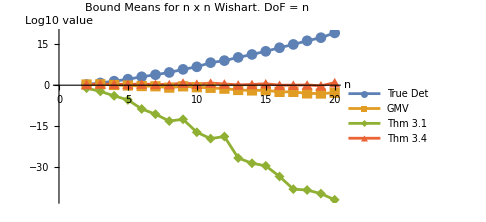

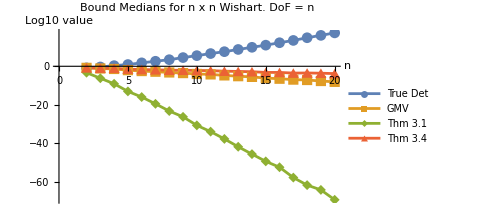

```mathematica
pMeansK1=ListLinePlot[Transpose[Table[{i+1,Log10[k1means[[i,j]]]},{i,1,len},{j,1,4}]],PlotLegends->Placed[labels,Right],PlotMarkers->Automatic,PlotLabel->"Bound Means for n x n Wishart. DoF = n",AxesLabel->{"n","Log10 value"},ImageSize->Medium]
pMedsK1=ListLinePlot[Transpose[Table[{i+1,Log10[k1meds[[i,j]]]},{i,1,len},{j,1,4}]],PlotLegends->Placed[labels,Right],PlotMarkers->Automatic,PlotLabel->"Bound Medians for n x n Wishart. DoF = n",AxesLabel->{"n","Log10 value"},ImageSize->Medium]
```

## k=2 Experiments

Generation of Data  for DoF = 2n

```mathematica
k2Seed=9729968;
SeedRandom[k2Seed];
ns=2;
ne=20;
k=2;
iters=1000;
len=ne-ns+1;
PSDsn2N20K2=WishartPairsN[ns,ne,k,iters];
DetBoundsK2=Table[DetBounds[PSDsn2N20K2[[i]]],{i,len}];
k2means=Table[Map[Mean,DetBoundsK2[[i]]],{i,len}];
k2meds=Table[Map[Median,DetBoundsK2[[i]]],{i,len}];
```

We verify that the bound of Theorem 3.4 achieves equality in the n=2 case and that it is dominated by the true determinant in all other cases. For each n we count the total number of cases where this holds. Since we run 1000 iterations for each n, we expect each of these values to be equal to 1000.

```mathematica
Total[Table[If[Abs[DetBoundsK2[[1,1,j]]-DetBoundsK2[[1,4,j]]]<10^(-12),1,0],{j,1,iters}]]
Total[Table[If[DetBoundsK2[[k,1,j]]>=DetBoundsK2[[k,4,j]],1,0],{j,1,iters},{k,2,len}]]
```

1000

{1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000}

Plotting Data. The first plot shows means and the second shows medians.

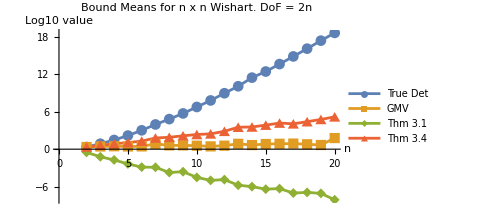

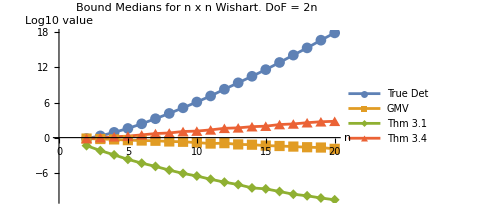

```mathematica
pMeansK2=ListLinePlot[Transpose[Table[{i+1,Log10[k2means[[i,j]]]},{i,1,len},{j,1,4}]],PlotLegends->Placed[labels,Right],PlotMarkers->Automatic,PlotLabel->"Bound Means for n x n Wishart. DoF = 2n",AxesLabel->{"n","Log10 value"},ImageSize->Medium]
pMedsK2=ListLinePlot[Transpose[Table[{i+1,Log10[k2meds[[i,j]]]},{i,1,len},{j,1,4}]],PlotLegends->Placed[labels,Right],PlotMarkers->Automatic,PlotLabel->"Bound Medians for n x n Wishart. DoF = 2n",AxesLabel->{"n","Log10 value"},ImageSize->Medium]
```

## k=4 Experiments

Generation of Data  for DoF = 4n

```mathematica
k4Seed=3526551;
SeedRandom[k4Seed];
ns=2;
ne=20;
k=4;
iters=1000;
len=ne-ns+1;
PSDsn2N20K4=WishartPairsN[ns,ne,k,iters];
DetBoundsK4=Table[DetBounds[PSDsn2N20K4[[i]]],{i,len}];
k4means=Table[Map[Mean,DetBoundsK4[[i]]],{i,len}];
k4meds=Table[Map[Median,DetBoundsK4[[i]]],{i,len}];
```

We verify that the bound of Theorem 3.4 achieves equality in the n=2 case and that it is dominated by the true determinant in all other cases. For each n we count the total number of cases where this holds. Since we run 1000 iterations for each n, we expect each of these values to be equal to 1000.

```mathematica
Total[Table[If[Abs[DetBoundsK4[[1,1,j]]-DetBoundsK4[[1,4,j]]]<10^(-12),1,0],{j,1,iters}]]
Total[Table[If[DetBoundsK4[[k,1,j]]>=DetBoundsK4[[k,4,j]],1,0],{j,1,iters},{k,2,len}]]
```

1000

{1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000}

Plotting Data. The first plot shows means and the second shows medians.

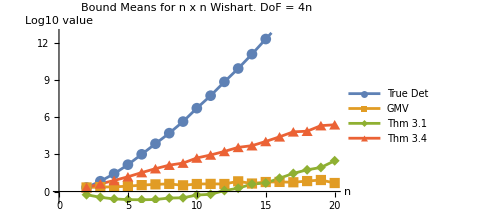

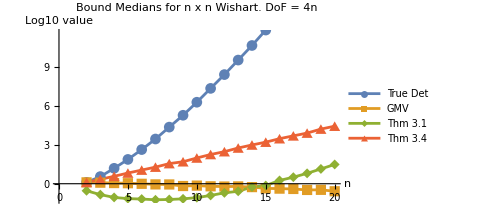

```mathematica
pMeansK4=ListLinePlot[Transpose[Table[{i+1,Log10[k4means[[i,j]]]},{i,1,len},{j,1,4}]],PlotLegends->Placed[labels,Right],PlotMarkers->Automatic,PlotLabel->"Bound Means for n x n Wishart. DoF = 4n",AxesLabel->{"n","Log10 value"},ImageSize->Medium]
pMedsK4=ListLinePlot[Transpose[Table[{i+1,Log10[k4meds[[i,j]]]},{i,1,len},{j,1,4}]],PlotLegends->Placed[labels,Right],PlotMarkers->Automatic,PlotLabel->"Bound Medians for n x n Wishart. DoF = 4n",AxesLabel->{"n","Log10 value"},ImageSize->Medium]
```

## k=8 Experiments

Generation of Data  for DoF = 8n

```mathematica
k8Seed=8310099;
SeedRandom[k8Seed];
ns=2;
ne=20;
k=8;
iters=1000;
len=ne-ns+1;
PSDsn2N20K8=WishartPairsN[ns,ne,k,iters];
DetBoundsK8=Table[DetBounds[PSDsn2N20K8[[i]]],{i,len}];
k8means=Table[Map[Mean,DetBoundsK8[[i]]],{i,len}];
k8meds=Table[Map[Median,DetBoundsK8[[i]]],{i,len}];
```

We verify that the bound of Theorem 3.4 achieves equality in the n=2 case and that it is dominated by the true determinant in all other cases. For each n we count the total number of cases where this holds. Since we run 1000 iterations for each n, we expect each of these values to be equal to 1000.

```mathematica
Total[Table[If[Abs[DetBoundsK8[[1,1,j]]-DetBoundsK8[[1,4,j]]]<10^(-12),1,0],{j,1,iters}]]
Total[Table[If[DetBoundsK8[[k,1,j]]>=DetBoundsK8[[k,4,j]],1,0],{j,1,iters},{k,2,len}]]
```

1000

{1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000}

Plotting Data. The first plot shows means and the second shows medians.

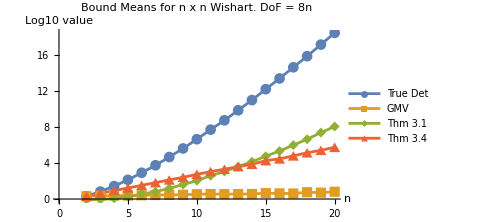

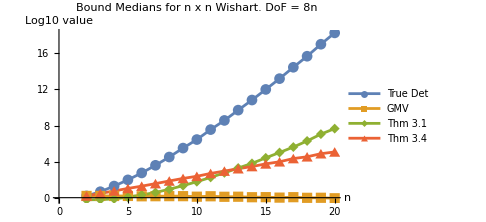

```mathematica
pMeansK8=ListLinePlot[Transpose[Table[{i+1,Log10[k8means[[i,j]]]},{i,1,len},{j,1,4}]],PlotLegends->Placed[labels,Right],PlotMarkers->Automatic,PlotLabel->"Bound Means for n x n Wishart. DoF = 8n",AxesLabel->{"n","Log10 value"},ImageSize->Medium]
pMedsK8=ListLinePlot[Transpose[Table[{i+1,Log10[k8meds[[i,j]]]},{i,1,len},{j,1,4}]],PlotLegends->Placed[labels,Right],PlotMarkers->Automatic,PlotLabel->"Bound Medians for n x n Wishart. DoF = 8n",AxesLabel->{"n","Log10 value"},ImageSize->Medium]
```